ЛР 4
гр. 351003
Вариант 9
Номер 1
Условие:
Создать таблицу значений функции f(x), разбив отрезок [0; 6] на n равных частей точками x_i (i = OverBar[0,n]). Для полученной таблично заданной в равноотстоящих узлах функции f(x), выполнить следующие действия при n = 6 и n = 10:
а) построить интерполяционный многочлен Лагранжа L_n(x) ,
проиллюстрировать графически (изобразить точки (x_i, f(x_i)) и графики функций f(x) и L_n(x) на одном чертеже);
б) создать таблицу конечных разностей функции f(x) по точкам (x_i, f(x_i)), i = OverBar[0,n];
в) построить второй интерполяционный многочлен Ньютона P_n(x),
проиллюстрировать графически;
г) построить интерполяционный многочлен Ньютона Np_n(x) с помощью функции InterpolatingPolynomial пакета Mathematica,
проиллюстрировать графически;
д) вычислить значения функции f(x) и всех построенных
интерполяционных многочленов L_n(x) , P_n(x) и Np_n(x) в точке
x = 2,4316;
е) построить график погрешности интерполирования многочленом Ньютона R_n(x) = |f(x) - Np_n(x)| на отрезке [0; 6], найти максимум погрешности R_n(x) на отрезке [0, 6] с помощью функции FindMaximum пакета Mathematica;
ж) исследовать зависимость погрешности интерполирования R_n(x) от
числа узлов интерполяции (степени многочлена n).

Функция f(x):

```mathematica
f[x_]=3+(2/7 x-Cosh[(3x)/13]) Log[x^2+2 x+3]
```

3+((2 x)/7-Cosh[(3 x)/13]) Log[3+2 x+x^2]

Значения из условия задания и шаги интерполяции h1 и h2 для равноотстоящих узлов:

```mathematica
a=0;b=6;n1=6;n2=10;x0=2.4316;h1=(b-a)/n1;h2=(b-a)/n2;
```

График функции f(x):

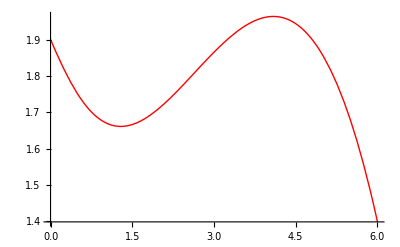

```mathematica
graph=Plot[f[x],{x,a,b},PlotStyle->{Red,Thick}]
```

Создадим таблицы значений функции для равноотстоящих узлов на промежутке для n1 и n2:

```mathematica
data1=Table[{i h1,f[i h1]},{i,0,n1}]//N
```

```mathematica
data2=Table[{i h2,f[i h2]},{i,0,n2}]//N
```

```mathematica
{TableForm[data1],TableForm[data2]}
```

{0. | 1.90139
1. | 1.67225
2. | 1.71237
3. | 1.86632
4. | 1.96411
5. | 1.85663
6. | 1.39751,0. | 1.90139
0.6 | 1.72822
1.2 | 1.66226
1.8 | 1.68933
2.4 | 1.77043
3. | 1.86632
3.6 | 1.94154
4.2 | 1.96364
4.8 | 1.90147
5.4 | 1.72369
6. | 1.39751}

a)

Введём вспомогательные обозначения Pl1(x) и Pl2(x):

```mathematica
Pl1[x_]=∏_(i=0)^n1 (x-data1[[i+1,1]])
```

(-6.+x) (-5.+x) (-4.+x) (-3.+x) (-2.+x) (-1.+x) (0.+x)

```mathematica
Pl2[x_]=∏_(i=0)^n2 (x-data2[[i+1,1]])
```

(-6.+x) (-5.4+x) (-4.8+x) (-4.2+x) (-3.6+x) (-3.+x) (-2.4+x) (-1.8+x) (-1.2+x) (-0.6+x) (0.+x)

Используя заданные обозначения, зададим формулы интерполяционного многочлена Лагранжа для n1 и n2:

```mathematica
Ln1[x_]=Sum[data1[[i+1,2]] Pl1[x]/((x-data1[[i+1,1]]) Pl1'[data1[[i+1,1]]]),{i,0,n1}]//Simplify
```

1.90139-0.395936 x+0.170555 x^2+0.00478091 x^3-0.009873 x^4+0.00140961 x^5-0.0000743014 x^6

```mathematica
Ln2[x_]=Sum[data2[[i+1,2]] Pl2[x]/((x-data2[[i+1,1]]) Pl2'[data2[[i+1,1]]]),{i,0,n2}]//Simplify
```

1.90139-0.352987 x+0.0499057 x^2+0.142218 x^3-0.0954616 x^4+0.0342697 x^5-0.008309 x^6+0.00136977 x^7-0.0001473 x^8+9.30508×10^-6 x^9-2.61522×10^-7 x^10

Изобразим полученные интерполяционные многочлены.

Интерполяционный многочлен Лагранжа для n = 6:

```mathematica
graph1D=ListPlot[data1,PlotStyle->{Darker,PointSize[0.02]}]
```

```mathematica
graph1Ln=Plot[Ln1[x],{x,a,b}]
```

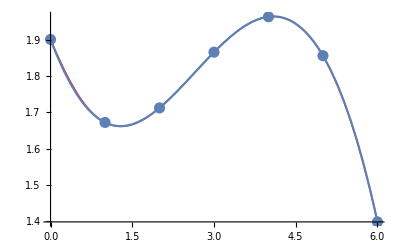

```mathematica
Show[graph,graph1D,graph1Ln]
```

Интерполяционный многочлен Лагранжа для n = 10:

```mathematica
graph2D=ListPlot[data2,PlotStyle->{Darker,PointSize[0.02]}]
```

```mathematica
graph2Ln=Plot[Ln2[x],{x,a,b}]
```

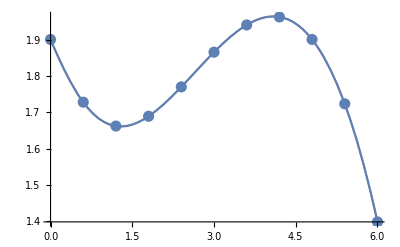

```mathematica
Show[graph,graph2D,graph2Ln]
```

б)

Представим таблицу конечных разностей функции f(x) в виде матрицы, каждый столбец которой соответствует конечным разностям соответствующего порядка от 0 до n - 1 (конечные разности 0-го порядка - значения функции в точках  x_i).

Для n = 6:

```mathematica
diftab1=Array[dif1,{n1+1,n1+1},{0,0}]
```

Поскольку с увеличением порядка конечных разностей их количество уменьшается, заполним пустые клетки таблицы:

```mathematica
For[k=1,k≤n1,k++,For[i=n1,i≥n1-k,i--,dif1[i,k]=""]]
```

```mathematica
For[i=0,i≤n1,i++,dif1[i,0]=data1[[i+1,2]]]
```

```mathematica
For[k=1,k≤n1,k++,For[i=0,i≤n1-k,i++,dif1[i,k]=dif1[i+1,k-1]-dif1[i,k-1]]]
```

```mathematica
PaddedForm[TableForm[diftab1],{n1,n1-1}]
```

1.90139 | -0.22914 |  0.26925 | -0.15542 | -0.01456 |  0.03541 | -0.05350
 1.67225 |  0.04012 |  0.11383 | -0.16998 |  0.02085 | -0.01809 | 
 1.71237 |  0.15395 | -0.05615 | -0.14913 |  0.00277 |  | 
 1.86632 |  0.09780 | -0.20528 | -0.14636 |  |  | 
 1.96411 | -0.10748 | -0.35164 |  |  |  | 
 1.85663 | -0.45912 |  |  |  |  | 
 1.39751 |  |  |  |  |  |

Аналогичным образом заполним таблицу для n = 10:

```mathematica
diftab2=Array[dif2,{n2+1,n2+1},{0,0}]
```

```mathematica
For[k=1,k≤n2,k++,For[i=n2,i≥n2-k,i--,dif2[i,k]=""]]
```

```mathematica
For[i=0,i≤n2,i++,dif2[i,0]=data2[[i+1,2]]]
```

```mathematica
For[k=1,k≤n2,k++,For[i=0,i≤n2-k,i++,dif2[i,k]=dif2[i+1,k-1]-dif2[i,k-1]]]
```

```mathematica
PaddedForm[TableForm[diftab2],{n2,n2-1}]
```

1.901387711 | -0.173165887 |  0.107199659 | -0.014163442 | -0.024838579 |  0.024587808 | -0.020521754 |  0.015602583 | -0.011459635 |  0.008206276 | -0.005738299
 1.728221825 | -0.065966227 |  0.093036217 | -0.039002021 | -0.000250771 |  0.004066054 | -0.004919171 |  0.004142948 | -0.003253359 |  0.002467977 | 
 1.662255598 |  0.027069990 |  0.054034196 | -0.039252793 |  0.003815283 | -0.000853117 | -0.000776222 |  0.000889589 | -0.000785382 |  | 
 1.689325587 |  0.081104185 |  0.014781403 | -0.035437510 |  0.002962166 | -0.001629339 |  0.000113367 |  0.000104207 |  |  | 
 1.770429773 |  0.095885588 | -0.020656107 | -0.032475344 |  0.001332827 | -0.001515972 |  0.000217574 |  |  |  | 
 1.866315361 |  0.075229482 | -0.053131450 | -0.031142516 | -0.000183145 | -0.001298399 |  |  |  |  | 
 1.941544843 |  0.022098031 | -0.084273967 | -0.031325661 | -0.001481544 |  |  |  |  |  | 
 1.963642874 | -0.062175935 | -0.115599628 | -0.032807205 |  |  |  |  |  |  | 
 1.901466939 | -0.177775563 | -0.148406834 |  |  |  |  |  |  |  | 
 1.723691376 | -0.326182397 |  |  |  |  |  |  |  |  | 
 1.397508978 |  |  |  |  |  |  |  |  |  |

в)

Построим вторые интерполяционные многочлены Ньютона Pn1(x) и Pn2(x) для n1 = 6 и n2 = 10:

```mathematica
q1=(x-b)/h1;Pn1[x_]=dif1[n1,0];P1[q_]=1;
```

```mathematica
For[k=1,k≤n1,k++,P1[q_]=P1[q1]*(q1+k-1);Pn1[x_]=Pn1[x]+dif1[n1-k,k]/(k!) P1[q1]]
```

```mathematica
Pn1[x]//Simplify
```

1.90139-0.395936 x+0.170555 x^2+0.00478091 x^3-0.009873 x^4+0.00140961 x^5-0.0000743014 x^6

```mathematica
q2=(x-b)/h2;Pn2[x_]=dif2[n2,0];P2[q_]=1;
```

```mathematica
For[k=1,k≤n2,k++,P2[q_]=P2[q2]*(q2+k-1);Pn2[x_]=Pn2[x]+dif2[n2-k,k]/(k!) P2[q2]]
```

```mathematica
Pn2[x]//Simplify
```

1.90139-0.352987 x+0.0499057 x^2+0.142218 x^3-0.0954616 x^4+0.0342697 x^5-0.008309 x^6+0.00136977 x^7-0.0001473 x^8+9.30508×10^-6 x^9-2.61522×10^-7 x^10

Изобразим полученные интерполяционные многочлены.

Второй интерполяционный многочлен Ньютона для n = 6:

```mathematica
graph1Pn=Plot[Pn1[x],{x,a,b}]
```

```mathematica
Show[graph,graph1D,graph1Pn]
```

-Graphics-

Второй интерполяционный многочлен Ньютона для n = 10:

```mathematica
graph2Pn=Plot[Pn2[x],{x,a,b}]
```

```mathematica
Show[graph,graph2D,graph2Pn]
```

-Graphics-

в)

Интерполяционные многочлены Ньютона функции f(x) для n1 = 6 и n2 = 10, построенные встроенной функцией пакета Mathematica:

```mathematica
Npn1[x_]=InterpolatingPolynomial[data1,x]//Simplify
```

1.90139-0.395936 x+0.170555 x^2+0.00478091 x^3-0.009873 x^4+0.00140961 x^5-0.0000743014 x^6

```mathematica
Npn2[x_]=InterpolatingPolynomial[data2,x]//Simplify
```

1.90139-0.352987 x+0.0499057 x^2+0.142218 x^3-0.0954616 x^4+0.0342697 x^5-0.008309 x^6+0.00136977 x^7-0.0001473 x^8+9.30508×10^-6 x^9-2.61522×10^-7 x^10

Изобразим полученные интерполяционные многочлены.

Интерполяционный многочлен Ньютона для n = 6:

```mathematica
graph1Npn=Plot[Npn1[x],{x,a,b}]
```

```mathematica
Show[graph,graph1D,graph1Npn]
```

-Graphics-

Интерполяционный многочлен Ньютона для n = 10:

```mathematica
graph2Npn=Plot[Npn2[x],{x,a,b}]
```

```mathematica
Show[graph,graph2D,graph2Npn]
```

-Graphics-

Все из полученных интерполяционных многочленов в узлах интерполяции совпадают с изначальной функцией, следовательно, все из них могут считаться мало отличающимися от f(x).

д)

Значения интерполяционных многочленов Лагранжа в точке x0:

```mathematica
Print["Ln1[x0]=",Ln1[x0],", Ln2[x0]=",Ln2[x0]]
```

Ln1[x0]=1.77512, Ln2[x0]=1.77544

Значения вторых интерполяционных многочленов Ньютона в точке x0:

```mathematica
Print["Pn1[x0]=",Pn1[x0],", Pn2[x0]=",Pn2[x0]]
```

Pn1[x0]=1.77512, Pn2[x0]=1.77544

Значения интерполяционных многочленов Ньютона в точке x0:

```mathematica
Print["Npn1[x0]=",Npn1[x0],", Npn2[x0]=",Npn2[x0]]
```

Npn1[x0]=1.77512, Npn2[x0]=1.77544

Исходя из полученных графиков и значений в точке x0, отметим, что интерполяционные многочлены, полученные различными способами, либо совпадают полностью, либо имеют незначительные отличия.

е)

Исследуем погрешность интерполирования многочленом Ньютона при n = 6.

```mathematica
Rn1[x_]=Abs[f[x]-Npn1[x]]
```

График погрешности Rn1(x):

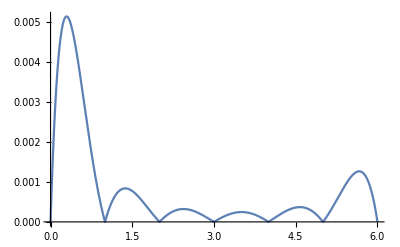

```mathematica
graphErr1=Plot[Rn1[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxErr1=FindMaximum[Rn1[x],{x,a,b}]
```

{0.00514607,{x→0.294199}}

Как видно из графика, максимальная погрешность интерполирования многочленом Ньютона при n = 6 находится на отрезке x ϵ [0; 1]. Результат, полученный функцией FindMaximum, соответствует графику.

Исследуем погрешность интерполирования многочленом Ньютона при n = 10.

```mathematica
Rn2[x_]=Abs[f[x]-Npn2[x]]
```

График погрешности Rn2(x):

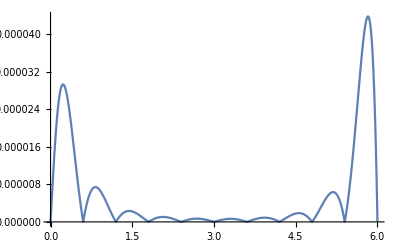

```mathematica
graphErr2=Plot[Rn2[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxErr2=FindMaximum[Rn2[x],{x,a,b}]
```

{0.0000292996,{x→0.229749}}

Как видно из графика, максимальная погрешность интерполирования многочленом Ньютона при n = 10 принадлежит отрезку x ϵ [5.4; 6]. В силу погрешности машинного сравнения рациональных чисел функция FindMaximum дала некорректный ответ.

Для получения более точного результата сузим промежуток значений аргумента:

```mathematica
maxErr2=FindMaximum[Rn2[x],{x,5.4,b}]
```

{0.0000437863,{x→5.82633}}

ж)

Исходя из полученных графиков погрешностей, можно сделать вывод, что с увеличением степени интерполяционного многочлена n погрешность интерполирования уменьшается (значение maxErr1 значительно больше значения maxErr2).